```mathematica
(*No Y; 10 Mags*)
fileX="C:\\Users\\jsten\\Documents\\Reaserch\\Majorana_spin\\The_Malcolm_Project\\B_Three Sections\\Profiles_2_21_2020\\John Box\\10 magnets\\Fixed\\NoY\\Bx_Average_10Mags_NoY_Fixed.txt";
fileY="C:\\Users\\jsten\\Documents\\Reaserch\\Majorana_spin\\The_Malcolm_Project\\B_Three Sections\\Profiles_2_21_2020\\John Box\\10 magnets\\Fixed\\NoY\\By_Average_10Mags_NoY_Fixed.txt";
```

```mathematica
(*Yes Y; 10 Mags*)
fileX="C:\\Users\\jsten\\Documents\\Reaserch\\Majorana_spin\\The_Malcolm_Project\\B_Three Sections\\Profiles_2_21_2020\\John Box\\10 magnets\\Fixed\\YesY\\Bx_Average_10Mags_YesY_Fixed.txt";
fileY="C:\\Users\\jsten\\Documents\\Reaserch\\Majorana_spin\\The_Malcolm_Project\\B_Three Sections\\Profiles_2_21_2020\\John Box\\10 magnets\\Fixed\\YesY\\By_Average_10Mags_YesY_Fixed.txt";
```

```mathematica
MagX={};
For[l=1,l≤151,l++,
out=Import[fileX,{"Lines",l}];
mtp=ToExpression[out];
MagX=Join[MagX,{mtp}];
];
```

```mathematica
MagY={};
For[l=1,l≤151,l++,
out=Import[fileY,{"Lines",l}];
mtp=ToExpression[out];
MagY=Join[MagY,{mtp}];
];
```

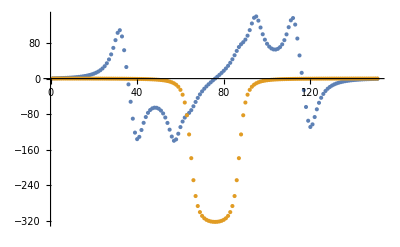

```mathematica
ListPlot[{MagX,MagY},PlotRange->All]
```

```mathematica
Clear[hbar, e0, m0, ηm];
hbar=6.58211899*10^(-16);  (* h/2π  in eV s *)
m0=9.10938215*10^(-31); 
e0=1.602176487*10^(-19);
ηm=hbar^2*e0*10^(20)/m0;  (* hbar^2/m0 in eV A^2 *)
μB=5.7883818066 * 10^(-2);    (* in meV/T *)
meVpK=8.6173325*10^(-2);   (* Kelvin into meV *)
(* **************************************** *)
```

```mathematica
Clear[ts, tsw, as, ms, Nx, Ny, Nxn, α, αw, Δ];
as=100.0; (* unit cell in A *)
ms=0.02;
ts=500*ηm/(2*as^2*ms); (* hopping in meV *)
α=200.0/as; (* Rashba coupling in meV *)
Δ=0.4; (* induced gap in meV *)
Nx=350-25;
NxM=50;
Nxn=0;
Ny=1;
asw=600.0/(Ny+1);
αw=α*as/asw*0;
tsw=4.0;
μ=0.0;
gx=0.02;
gy=0.02;
B=2Δ;

(*tϕ=ts/200;*)
tϕ1=0.4*ts;
tϕ2=ts;
αϕ=0.0;
```

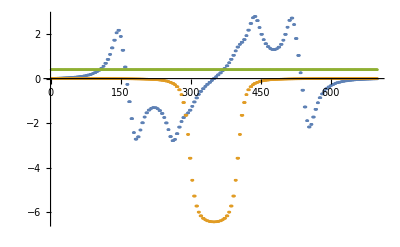

```mathematica
(*Currently MagΔ is being used*)
MagΔX=Table[gx*MagX[[Ceiling[ii*Length[MagX]/(2Nx+NxM)]]],{ii,1,2Nx+NxM}];
MagΔY=Table[gy*MagY[[Ceiling[ii*Length[MagY]/(2Nx+NxM)]]],{ii,1,2Nx+NxM}];
Gap=Table[Δ,{i,1,Length[MagΔX]}];

ListPlot[{MagΔX,MagΔY,Gap},PlotRange->All]
```

```mathematica
H[ϕ_]:=Block[{Hsp},
ϵ0=2ts Cos[Pi/(2Nx+NxM+1.0)];
(*First Chain*)
H1σ11τ11=SparseArray[{Band[{1,1}]->Table[-μ+ϵ0+MagΔY[[i]] ,{i,1,Nx}],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H1σ22τ11=SparseArray[{Band[{1,1}]->Table[-μ+ϵ0-MagΔY[[i]] ,{i,1,Nx}],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H1σ12τ11=SparseArray[{Band[{1,1}]->Table[MagΔX[[i]],{i,1,Nx}],Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{Nx,Nx}];
H1σ21τ11=SparseArray[{Band[{1,1}]->Table[MagΔX[[i]],{i,1,Nx}],Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{Nx,Nx}];

H1σ12τ12=SparseArray[{Band[{1,1}]->Δ},{Nx,Nx}];
H1σ21τ12=SparseArray[{Band[{1,1}]->-Δ},{Nx,Nx}];

H1τ11=SparseArray[ArrayFlatten[{{H1σ11τ11,H1σ12τ11},{H1σ21τ11,H1σ22τ11}}]];
H1τ22=-H1τ11;
H1τ12=SparseArray[ArrayFlatten[{{0,H1σ12τ12},{H1σ21τ12,0}}]];
H1τ21=Conjugate[Transpose[H1τ12]];

H11=SparseArray[ArrayFlatten[{{H1τ11,H1τ12},{H1τ21,H1τ22}}]];


(*Middle Chain*)
HMσ11τ11=SparseArray[{Band[{1,1}]->Table[-μ+ϵ0+MagΔY[[Nx+i]],{i,1,NxM}],Band[{1,2}]->ts,Band[{2,1}]->ts},{NxM,NxM}];
HMσ22τ11=SparseArray[{Band[{1,1}]->Table[-μ+ϵ0-MagΔY[[Nx+i]] ,{i,1,NxM}],Band[{1,2}]->ts,Band[{2,1}]->ts},{NxM,NxM}];
HMσ12τ11=SparseArray[{Band[{1,1}]->Table[MagΔX[[Nx+i]],{i,1,NxM}],Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{NxM,NxM}];
HMσ21τ11=SparseArray[{Band[{1,1}]->Table[MagΔX[[Nx+i]] ,{i,1,NxM}],Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{NxM,NxM}];

HMσ12τ12=SparseArray[{Band[{1,1}]->Δ ⅇ^(ⅈ ϕ)},{NxM,NxM}];
HMσ21τ12=SparseArray[{Band[{1,1}]->-Δ ⅇ^(ⅈ ϕ)},{NxM,NxM}];

HMτ11=SparseArray[ArrayFlatten[{{HMσ11τ11,HMσ12τ11},{HMσ21τ11,HMσ22τ11}}]];
HMτ22=-HMτ11;
HMτ12=SparseArray[ArrayFlatten[{{0,HMσ12τ12},{HMσ21τ12,0}}]];
HMτ21=Conjugate[Transpose[HMτ12]];

HMM=SparseArray[ArrayFlatten[{{HMτ11,HMτ12},{HMτ21,HMτ22}}]];


(*Second Chain*)
H2σ11τ11=SparseArray[{Band[{1,1}]->Table[-μ+ϵ0+MagΔY[[Nx+NxM+i]] ,{i,1,Nx}],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H2σ22τ11=SparseArray[{Band[{1,1}]->Table[-μ+ϵ0-MagΔY[[Nx+NxM+i]] ,{i,1,Nx}],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H2σ12τ11=SparseArray[{Band[{1,1}]->Table[MagΔX[[Nx+NxM+i]] ,{i,1,Nx}],Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{Nx,Nx}];
H2σ21τ11=SparseArray[{Band[{1,1}]->Table[MagΔX[[Nx+NxM+i]] ,{i,1,Nx}],Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{Nx,Nx}];

H2σ12τ12=SparseArray[{Band[{1,1}]->Δ ⅇ^(ⅈ ϕ)},{Nx,Nx}];
H2σ21τ12=SparseArray[{Band[{1,1}]->-Δ ⅇ^(ⅈ ϕ)},{Nx,Nx}];

H2τ11=SparseArray[ArrayFlatten[{{H2σ11τ11,H2σ12τ11},{H2σ21τ11,H2σ22τ11}}]];
H2τ22=-H2τ11;
H2τ12=SparseArray[ArrayFlatten[{{0,H2σ12τ12},{H2σ21τ12,0}}]];
H2τ21=Conjugate[Transpose[H2τ12]];

H22=SparseArray[ArrayFlatten[{{H2τ11,H2τ12},{H2τ21,H2τ22}}]];

(*Tunnel Junction*)
H1M=SparseArray[{{Nx,1}->tϕ1,{2Nx,NxM+1}->tϕ1,{3Nx,2NxM+1}->-tϕ1,{4Nx,3NxM+1}->-tϕ1},{4Nx,4NxM}];
HM1=Conjugate[Transpose[H1M]];

HM2=SparseArray[{{NxM,1}->tϕ2,{2NxM,Nx+1}->tϕ2,{3NxM,2Nx+1}->-tϕ2,{4NxM,3Nx+1}->-tϕ2},{4NxM,4Nx}];
H2M=Conjugate[Transpose[HM2]];

(*Full Wire*)
Hsp=SparseArray[ArrayFlatten[{{H11,H1M,0},{HM1,HMM,HM2},{0,H2M,H22}}]];

Hsp
];
```

```mathematica
H0=H[0.];
{e0,ψ0}=Transpose[Sort[Transpose[Eigensystem[H0,-10]]]];
```

```mathematica
e0
```

{-0.195913,-0.0349942,-0.0349661,-0.00117255,-6.76206×10^-7,6.76206×10^-7,0.00117255,0.0349661,0.0349942,0.195913}

```mathematica
eϕ={};
elϕ=Table[{},{n,1,10}];
For[ϕ=0,ϕ≤4π,ϕ+=0.1,


Hsp=H[ϕ];


etp=Sort[Eigenvalues[Hsp,-10]];
For[n=1,n≤Length[etp],n++,
elϕ[[n]]=Join[elϕ[[n]],{{ϕ,etp[[n]]}}]
];
If[π<ϕ<3π,
eϕ=Join[eϕ,{{ϕ,Sum[etp[[i]],{i,1,Length[etp]/2-2}]+etp[[Length[etp]/2+1]]+etp[[Length[etp]/2+2]]}}];
,
eϕ=Join[eϕ,{{ϕ,Sum[etp[[i]],{i,1,Length[etp]/2-2}]+etp[[Length[etp]/2-1]]+etp[[Length[etp]/2]]}}];
];


];


Iϕ={};
IϕM={};
For[ϕi=2,ϕi≤Length[eϕ],ϕi++,
Iϕ=Join[Iϕ,{{eϕ[[ϕi,1]],(eϕ[[ϕi,2]]-eϕ[[ϕi-1,2]])/(eϕ[[ϕi,1]]-eϕ[[ϕi-1,1]])}}];
IϕM=Join[IϕM,{Re[(eϕ[[ϕi,2]]-eϕ[[ϕi-1,2]])/(eϕ[[ϕi,1]]-eϕ[[ϕi-1,1]])]}];
];
```

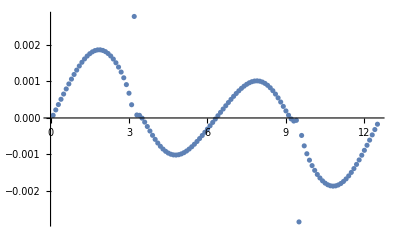

```mathematica
ListPlot[Re[Iϕ]]
```

```mathematica
IϕyesY=Iϕ;
```

```mathematica
IϕnoY=Iϕ;
```

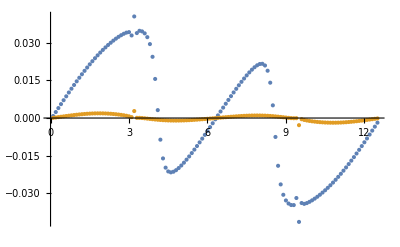

```mathematica
ListPlot[{Re[IϕyesY],Re[IϕnoY]}]
```

```mathematica
eyesY=e0;
```

```mathematica
enoY=e0;
```

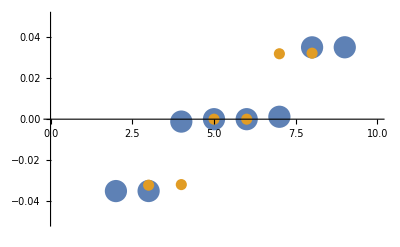

```mathematica
ListPlot[{enoY,eyesY},PlotStyle->{PointSize[0.04],PointSize[0.02]},PlotRange->{-0.05,0.05}]
```